```mathematica
串联耦合摆能谱的快速计算
```

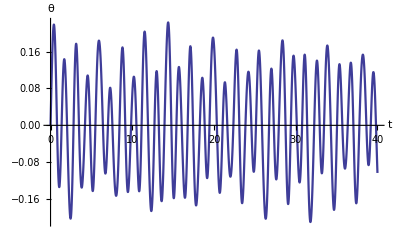

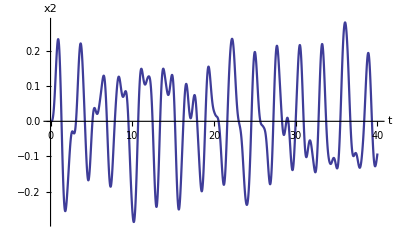

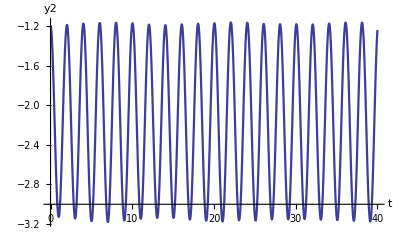

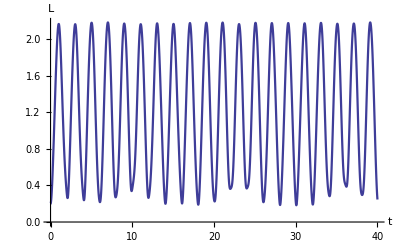

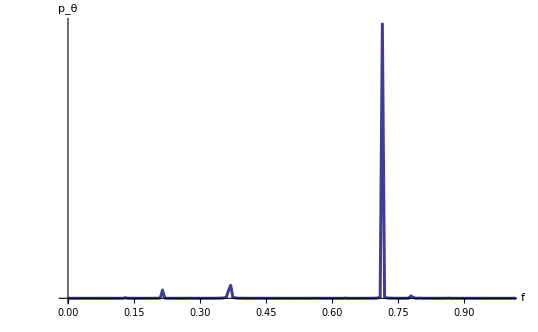

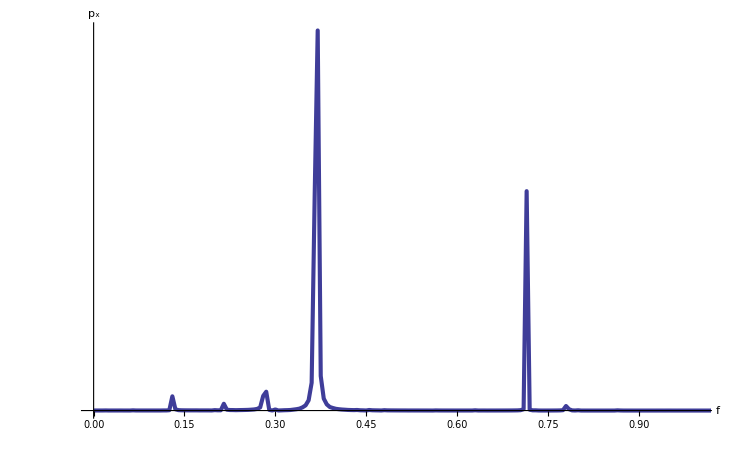

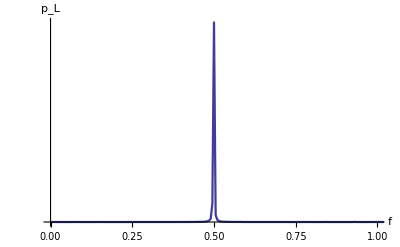

```mathematica
g=9.8;m1=0.1;m2=0.05;k=0.5;tm=200.0;
L1=1;         (*length of thread*)
L2=0.2;   (*initial length of spring*)
initial1={0,0.8/L1};
initial2={0,0.0,-(L1+L2),0};
P1=x2[t]^2+y2[t]^2+L1^2;
P2=2L1*(y2[t]*Cos[θ[t]]-x2[t]*Sin[θ[t]]);
L=√(P1+P2);(*length of spring*)
equ={θ''[t]==
k (y2[t] Sin[θ[t]]+x2[t] Cos[θ[t]]) 
*(1-L2/L) /(m1 L1)-g Sin[θ[t]]/L1,
x2''[t]==
-k (x2[t]-L1 Sin[θ[t]]) (1-L2/L)/m2,
y2''[t]==
-k (y2[t]+L1 Cos[θ[t]]) (1-L2/L)/m2-g,
θ[0]==initial1[[1]],θ'[0]==initial1[[2]],
x2[0]==initial2[[1]],x2'[0]==initial2[[2]],
y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};
s=NDSolve[equ,{θ,x2,y2},{t,0,tm},MaxSteps->∞];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];
(*.......................................*)
Plot[θ[t],{t,0,tm/5},PlotPoints->100,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"t","θ"},BaseStyle->{FontSize->13}]
Plot[x2[t],{t,0,tm/5},PlotPoints->100,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"t","x2"},BaseStyle->{FontSize->13}]
Plot[y2[t],{t,0,tm/5},PlotPoints->100,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"t","y2"},BaseStyle->{FontSize->13}]
Plot[L,{t,0,tm/5},PlotPoints->100,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"t","L"},BaseStyle->{FontSize->13}]
(*.......................................*)
sample=2000;
signal=Table[θ[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"f","p_θ"},BaseStyle->{FontSize->13}]

signal=Table[x2[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"f","p_x"},BaseStyle->{FontSize->13}]

average=Sum[L,{t,0,tm,tm/sample}]/sample;
signal=Table[(L-average),{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
AxesLabel->{"f","p_L"},BaseStyle->{FontSize->13}]

Clear[θ,x2,y2,signal,ps,fs]
```